```mathematica
params = {1,1,1,1,1,1,1,1,1,2,1}
```

{1,1,1,1,1,1,1,1,1,2,1}

```mathematica
F[x_,y_,p0_,p1_,p2_,p3_,p4_,p5_,p6_,p7_,p8_,p9_,p10_]:=p8*Tanh[(p2*(x+p0)+p3(y+p1)+p6)]+p9*Tanh[(p4(x+p0)+p5*(y+p1)+p7)]+p10
```

```mathematica
dxu1k[x_,y_,p0_,p1_,p2_,p3_,p4_,p5_,p6_,p7_,p8_,p9_,p10_] = D[F[x,y,p0,p1,p2,p3,p4,p5,p6,p7,p8,p9,p10],x]
```

p2 p8 Sech[p6+p2 (p0+x)+p3 (p1+y)]^2+p4 p9 Sech[p7+p4 (p0+x)+p5 (p1+y)]^2

```mathematica
dxdpiphi[x_,y_,p0_,p1_,p2_,p3_,p4_,p5_,p6_,p7_,p8_,p9_,p10_] = D[F[x,y,p0,p1,p2,p3,p4,p5,p6,p7,p8,p9,p10],x,p6]
```

-2 p2 p8 Sech[p6+p2 (p0+x)+p3 (p1+y)]^2 Tanh[p6+p2 (p0+x)+p3 (p1+y)]

```mathematica
a =
Integrate[dxu1k[x,-Pi,Sequence@@params]*dxdpiphi[x,-Pi,Sequence @@ params], {x,-Pi,Pi}]
```

3/2 (Sech[3]^4-Sech[3-2 π]^4)

```mathematica
b=Integrate[dxu1k[x,Pi,Sequence@@params]*dxdpiphi[x,Pi,Sequence@@params], {x,-Pi,Pi}]
```

-3/2 (Sech[3]^4-Sech[3+2 π]^4)

```mathematica
dyu1k[x_,y_,p0_,p1_,p2_,p3_,p4_,p5_,p6_,p7_,p8_,p9_,p10_] = D[F[x,y,p0,p1,p2,p3,p4,p5,p6,p7,p8,p9,p10],y]
```

p3 p8 Sech[p6+p2 (p0+x)+p3 (p1+y)]^2+p5 p9 Sech[p7+p4 (p0+x)+p5 (p1+y)]^2

```mathematica
dydpiphi[x_,y_,p0_,p1_,p2_,p3_,p4_,p5_,p6_,p7_,p8_,p9_,p10_] = D[F[x,y,p0,p1,p2,p3,p4,p5,p6,p7,p8,p9,p10],y,p6]
```

-2 p3 p8 Sech[p6+p2 (p0+x)+p3 (p1+y)]^2 Tanh[p6+p2 (p0+x)+p3 (p1+y)]

```mathematica
c=Integrate[dyu1k[-Pi,y,Sequence@@params]*dydpiphi[-Pi,y,Sequence@@params], {y,-Pi,Pi}]
```

3/2 (Sech[3]^4-Sech[3-2 π]^4)

```mathematica
d=Integrate[dyu1k[Pi,y,Sequence@@params]*dydpiphi[Pi,y,Sequence @@ params], {y,-Pi,Pi}]
```

-3/2 (Sech[3]^4-Sech[3+2 π]^4)

```mathematica
N[a+b+c+d]
```

-0.0000944761

```mathematica
N[a]
```

0.00009877

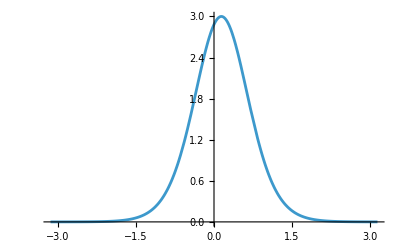

```mathematica
Plot[dxu1k[x,-Pi,Sequence@@params]*dxdp8phi[x,-Pi,Sequence @@ params], {x,-Pi,Pi}]
```

```mathematica
temp[x_]:=dxu1k[x,-Pi,Sequence@@params]*dxdpiphi[x,-Pi,Sequence @@ params]
```

```mathematica
N[Pi/6*(temp[-Pi]+4*temp[-Pi/2]+2*temp[0]+4*temp[Pi/2]+temp[Pi])]
```

0.552759

```mathematica
temp2[x_]:=dxu1k[x,Pi,Sequence@@params]*dxdpiphi[x,Pi,Sequence @@ params]
```

```mathematica
N[Pi/6*(temp2[-Pi]+4*temp2[-Pi/2]+2*temp2[0]+4*temp2[Pi/2]+temp2[Pi])]
```